# Nonlinear Mechanics and Chaos

## Juan Jose Neri

### Problem 12.7

-Graphics-

#### Using equation (12-11)

Θ''+2 β Θ'+w_0^2 sin(Θ)=γ w_0^2 cos(w t)

#### And the values stated in the problem description

```mathematica
w=2Pi;
w0=3/2w;
β=w0/4;
γ=0.9;
```

#### Now solve the differential equations numerically

```mathematica
NDSolve[{
Θ''[t]+2 *β* Θ'[t]+w0^2 *Sin[Θ[t]]==γ *w0^2 *Cos[w t],
Θ[0]==0,
Θ'[0]==0
},Θ,{t,0,6}]
```

{{Θ→InterpolatingFunction[{{0., 6.}}, <>]}}

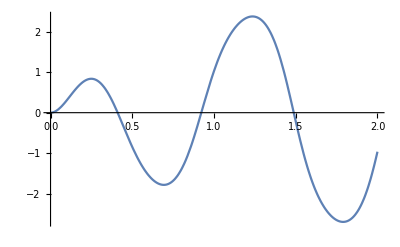

```mathematica
Plot[Evaluate[Θ[t]/.%],{t,0,2}]
```

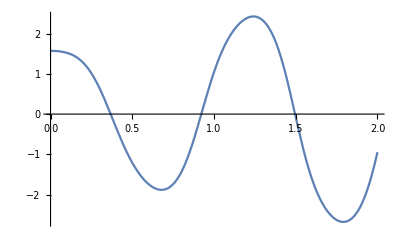

```mathematica
NDSolve[{
Θ''[t]+2 *β* Θ'[t]+w0^2 *Sin[Θ[t]]==γ *w0^2 *Cos[w t],
Θ[0]==Pi/2,
Θ'[0]==0
},Θ,{t,0,6}];
Plot[Evaluate[Θ[t]/.%],{t,0,2}]
```

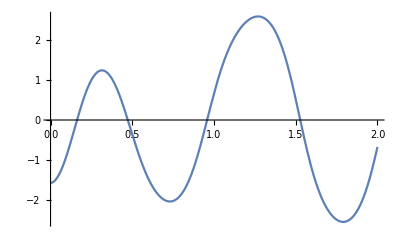

```mathematica
NDSolve[{
Θ''[t]+2 *β* Θ'[t]+w0^2 *Sin[Θ[t]]==γ *w0^2 *Cos[w t],
Θ[0]==-Pi/2,
Θ'[0]==0
},Θ,{t,0,6}];
Plot[Evaluate[Θ[t]/.%],{t,0,2}]
```

#### All in the same pair of axes

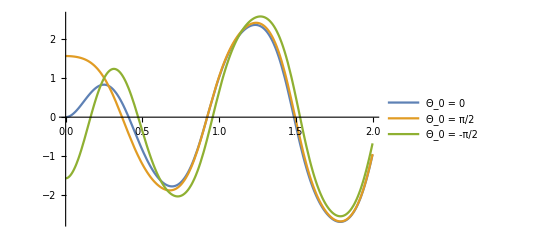

```mathematica
NDSolve[{
x''[t]+2 *β* x'[t]+w0^2 *Sin[x[t]]==γ *w0^2 *Cos[w t],
y''[t]+2 *β* y'[t]+w0^2 *Sin[y[t]]==γ *w0^2 *Cos[w t],
z''[t]+2 *β* z'[t]+w0^2 *Sin[z[t]]==γ *w0^2 *Cos[w t],
x[0]==0,
x'[0]==0,
y[0]==Pi/2,
y'[0]==0,
z[0]==-Pi/2,
z'[0]==0
},{x,y,z},{t,0,6}];
Plot[Evaluate[{x[t],y[t],z[t]}/.%],{t,0,2},PlotLegends->{"Θ_0 = 0","Θ_0 = π/2","Θ_0 = -π/2"}]
```

#### All solutions approach the same period after time t = 3